# A brief introduction to probability

## Why do we need probability?

Consider a game in which you win a prize if you get an object from the “Win” class or lose if you get an object from the “Lose” class. All you know is some of the objects in each class. You don’t know all objects in each class!

Imagine that you play and obtain one of the following objects.

Can you certainly tell if you win or lose? One could use a classifier to decide but the decision is not easy in all cases...

The heart does not appear in any of the examples but most blue objects are in the Win class. You might reasonably conclude that you win if you get a blue heart.

The yellow circle and blue cloud are more difficult to classify...

The most reasonable is to talk about the chances that a previously unseen object is in each class. 

Probability allows us to formalise and quantify the concept of chance.

## Basics: Experiments and events

Experiment (or trial): Action which results in one of several possible outcomes.

Examples: Toss a coin, Toss a six-sided dice...

Sample space: Set of all possible outcomes of the experiment.

Often denoted by Ω (Greek capital “omega”)

Example: For a coin, Ω={Heads, Tails}

Event: Collection of outcomes of an experiment (elements from Ω)

Denoted by capital letters: A, B, C ...

Empty event: Contains no outcomes (denoted as ∅)

Example: Toss a six-sided die and obtain an odd number. The event is A={1,3,5}.

## Probability

Rough definition: The probability of an event of a random experiment is a number between 0 and 1 which measures the likelihood of the event occurring when the experiment is performed.

The probability of an event A is denoted by P(A)

### Probability as a relative frequency

Assume that experiments can be repeated in identical conditions:

Some regularity between different experiments.

n_T: Number of trials

n_A: Number of times the event A is observed.

The relative frequency of event A: n_A/n_T

Frequentist interpretation of probability:

The probability of A is the relative frequency of A in the limit of infinite number of trials.

P(A)=lim_(n_T→ ∞) n_A/n_T

### Example: Tossing a fair coin

Two events: H (``heads’’) and T (``tails’’)

Abstraction:  P(H)=1/2 and P(T)=1/2

How good is the abstraction?

Simulate experiments with a large number of trials.

The relative frequency of H tends to 1/2 but one needs many trials.

#### Simulating one experiment

Let us simulate 10 trials (Heads: 0, Tails: 1)

```mathematica
sample=RandomInteger[{0,1},10]
```

{1,1,1,0,0,1,0,0,0,0}

```mathematica
Counts[sample]
```

<|1→4,0→6|>

```mathematica
count=KeySort[Counts[sample]]
```

<|0→6,1→4|>

Frequency of heads:

```mathematica
freq=count[[2]]/10
```

2/5

Aside: Here, we use 0/1 for H/T but one could also use “H” and “T”:

```mathematica
count2=RandomChoice[{"H","T"},10]
```

{H,H,H,T,H,H,H,T,H,T}

The actual way to represent the outcomes is not so important. Their frequency is important.

#### Simulating many experiments

Let us define a function that gives the relative frequency of heads in a series of n trials:

```mathematica
relfreq[n_]:=Module[{n0=n,count1,freq1},count1=KeySort[Counts[RandomInteger[{0,1},n0]]];
freq1=count1[[2]]/n0];
```

```mathematica
relfreq[10]
```

2/5

We then look at the relative frequency of H for experiments with increasing number of trials, starting from an experiment with 5 trials:

```mathematica
Maxexp=1000;  (* Maximum number of trials *)
```

```mathematica
rfn=Table[{nT,relfreq[nT]},{nT,5,Maxexp}];
```

```mathematica
rfn
```

{{5,4/5},{6,1/2},{7,5/7},{8,1/4},{9,7/9},{10,2/5},{11,5/11},{12,5/12},{13,5/13},{14,3/7},{15,7/15},{16,7/16},{17,9/17},{18,5/9},{19,10/19},{20,1/2},{21,5/21},{22,1/2},{23,11/23},{24,1/2},{25,12/25},{26,7/13},{27,5/9},{28,15/28},{29,15/29},{30,2/3},{31,15/31},{32,11/16},{33,7/11},{34,1/2},{35,18/35},{36,5/9},{37,14/37},{38,8/19},{39,23/39},{40,9/20},{41,19/41},{42,2/3},{43,27/43},{44,5/11},{45,26/45},{46,21/46},{47,28/47},{48,11/24},{49,23/49},{50,11/25},{51,28/51},{52,29/52},{53,25/53},{54,4/9},{55,32/55},{56,1/2},{57,9/19},{58,14/29},{59,32/59},{60,31/60},{61,28/61},{62,1/2},{63,13/21},{64,35/64},{65,34/65},{66,29/66},{67,31/67},{68,15/34},{69,35/69},{70,16/35},{71,38/71},{72,37/72},{73,40/73},{74,1/2},{75,37/75},{76,21/38},{77,38/77},{78,37/78},{79,36/79},{80,39/80},{81,38/81},{82,39/82},{83,43/83},{84,23/42},{85,44/85},{86,1/2},{87,50/87},{88,47/88},{89,36/89},{90,41/90},{91,43/91},{92,61/92},{93,40/93},{94,39/94},{95,39/95},{96,53/96},{97,52/97},{98,23/49},{99,52/99},{100,11/25}}

A simple plot of the results:

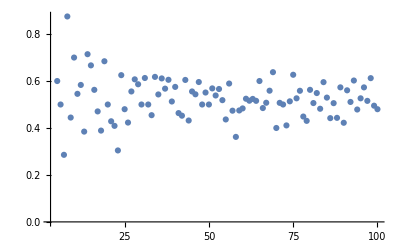

```mathematica
ListPlot[rfn,PlotRange->All]
```

A more elaborate plot:

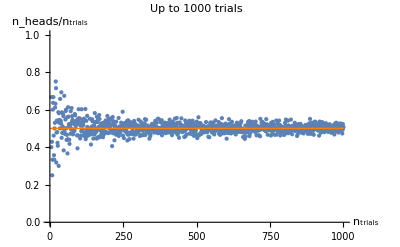

```mathematica
Show[{ListPlot[rfn,PlotStyle->PointSize[Large], AxesLabel->{"n_trials","n_heads/n_trials"},PlotRange->{0,1},BaseStyle->{FontSize->Scaled[.045]},PlotLabel->Style["Up to "<>ToString[Maxexp]<>" trials",FontSize->16]],Plot[0.5,{x,1,Maxexp},PlotStyle->{Orange,Thick}]}]
```

The value P(H)=1/2 is only obtained with certainty for infinitely many trials.

If we repeat experiments with n trials many times, the dispersion of the results for n_H/n_T decreases with increasing n_T

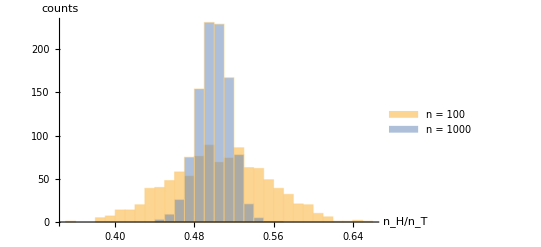

```mathematica
Histogram[{Table[relfreq[100],{i,1,1000}],Table[relfreq[1000],{i,1,1000}]},ChartLegends->{"n = 100","n = 1000"},AxesLabel->{"n_H/n_T","counts"}]
```